```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nathan/QEA-Eigenfaces/Eigenfaces

```mathematica
components=Map[eigenCompress[#1,eigenfaces[[2;;3]],All]&,images];
components=Partition[components,8];
components=MapThread[Labeled[#1,#2]&,{components,names}];
```

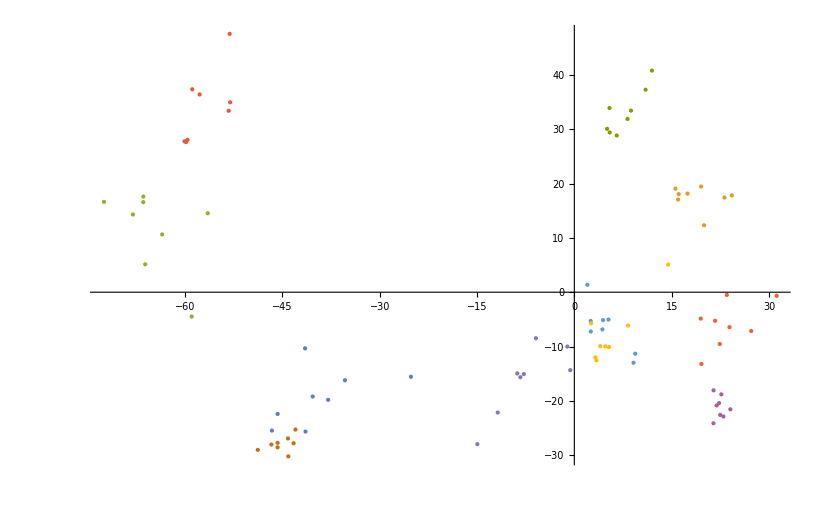

```mathematica
ListPlot[components[[10;;20]],PlotStyle->PointSize[Large],ImageSize->Large]
```

```mathematica
components3=Map[eigenCompress[#1,eigenfaces[[2;;4]],All]&,images];
components3=Partition[components3,8];
(*components3=MapThread[Labeled[#1,#2]&,{components3,names}];*)
ListPointPlot3D[components3[[20;;40]],PlotStyle->PointSize[Large],ImageSize->Large]
```

-Graphics3D-